```mathematica
n = 30;
nodes=Table[x[i-1]->NRoots[LegendreP[n+1, x]==0,x][[i,2]],{i,1,n+1}]
```

{x[0]→-0.997087,x[1]→-0.984686,x[2]→-0.962504,x[3]→-0.930757,x[4]→-0.88976,x[5]→-0.83992,x[6]→-0.781733,x[7]→-0.715777,x[8]→-0.642707,x[9]→-0.563249,x[10]→-0.478194,x[11]→-0.388386,x[12]→-0.294718,x[13]→-0.198121,x[14]→-0.0995553,x[15]→0.,x[16]→0.0995553,x[17]→0.198121,x[18]→0.294718,x[19]→0.388386,x[20]→0.478194,x[21]→0.563249,x[22]→0.642707,x[23]→0.715777,x[24]→0.781733,x[25]→0.83992,x[26]→0.88976,x[27]→0.930757,x[28]→0.962504,x[29]→0.984686,x[30]→0.997087}

```mathematica
fx = Table[{x[i], 0},{i,0,n}]/.nodes;
fx[[16,2]] = 1;
fx
```

{{-0.997087,0},{-0.984686,0},{-0.962504,0},{-0.930757,0},{-0.88976,0},{-0.83992,0},{-0.781733,0},{-0.715777,0},{-0.642707,0},{-0.563249,0},{-0.478194,0},{-0.388386,0},{-0.294718,0},{-0.198121,0},{-0.0995553,0},{0.,1},{0.0995553,0},{0.198121,0},{0.294718,0},{0.388386,0},{0.478194,0},{0.563249,0},{0.642707,0},{0.715777,0},{0.781733,0},{0.83992,0},{0.88976,0},{0.930757,0},{0.962504,0},{0.984686,0},{0.997087,0}}

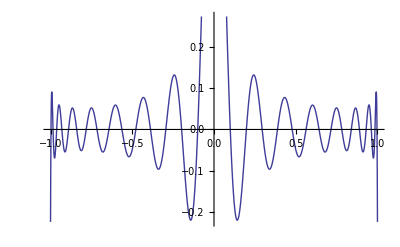

```mathematica
Plot[InterpolatingPolynomial[fx,x],{x,-1,1}]
```